## Import data from inSpire HEP

Download and extract the JSON file: inSpire.json

Transform it as a list of associations

```mathematica
data=Part[
Reap[
Module[
{line,file=FileNameJoin[{NotebookDirectory[], "inSpire.json"}]},Quiet@Close[file];
OpenRead[file];
While[line=!=EndOfFile,line=ReadString[file,"\n"];
Replace[line,_String:>Sow@Developer`ReadRawJSONString[line]]];
]
],
2,1
];
```

Create the inSpire.mx and save it with the symbol “data”:

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\olive\Desktop

```mathematica
DumpSave["inSpire.mx",data]
```

{{<|free_keywords→{},standardized_keywords→{},citations→{452267,1520868,275304,524107,76215,311629,366639,846024,151315,838517,139190,81651,128250},recid→1,title→Isoclinic N planes in Euclidean 2N space, Clifford parallels in elliptic (2N-1) space, and the Hurwitz matrix equations,references→{1256272,51394},abstract→1086,authors→{Wong, Yung-Chow},creation_date→1961,co-authors→{}|>,1226157,<|free_keywords→{},standardized_keywords→{},citations→{},recid→1604161,title→87,1,abstract→919,authors→{Dhuria, Mansi},creation_date→2016,co-authors→{}|>}}
 |  |  |  |

## Import database

### Database

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\olive\Desktop\WSS17_project

We get the database inSpire.mx

```mathematica
<<inSpire.mx
```

```mathematica
Length[data]
```

1226159

It contains 1226159 papers!

Each element is a list of associations of this type:

```mathematica
Dataset[data[[5444]]]
```

Dataset[<>]

We define new keys for later convenience:

```mathematica
Clear[tmpdata,pubdata]
```

```mathematica
rules=#->StringJoin@Map[Capitalize,StringSplit[#,"_"|"-"]]&/@Keys@{"free_keywords"->"freekeys","standardized_keywords"->"StandardKeys","creation_date"->"creationdate", "co-authors"->"coauthors"}
```

{free_keywords→FreeKeywords,standardized_keywords→StandardizedKeywords,creation_date→CreationDate,co-authors→CoAuthors}

```mathematica
tmpdata=KeyMap[ReplaceAll[rules]]/@data;
```

```mathematica
Dataset[tmpdata[[1124342]]]
```

Dataset[<>]

We notice that some entries have incorrect CreationDate values...we are going to correct them:

```mathematica
Cases[tmpdata[[All,"CreationDate"]],x_String/;StringMatchQ[x,"*/*"]]
```

{2006/2007,2013/04/18,1965/10,1965/08/15,1966/05/04,2007/06,2013/2014,2014/02/24}

```mathematica
Position[tmpdata[[All,"CreationDate"]],x_String/;StringMatchQ[x,"*/*"]]
```

{{770264},{998305},{1012583},{1012724},{1012725},{1018169},{1046050},{1133161}}

```mathematica
Cases[tmpdata[[All,"CreationDate"]],x_String/;StringMatchQ[x,"*-0-0*"]]
```

{1997-0-0}

```mathematica
Position[tmpdata[[All,"CreationDate"]],x_String/;StringMatchQ[x,"*-0-0"]]
```

{{977163}}

```mathematica
Position[tmpdata[[All,"CreationDate"]],x_String/;StringMatchQ[x,"0 2004"]]
```

{{1223323}}

We assign the correct value (after checking on inSpire)

```mathematica
tmpdata[[770264,"CreationDate"]]={2008,08};
tmpdata[[1046050,"CreationDate"]]={2013};
tmpdata[[977163,"CreationDate"]]={2012,11,07};
tmpdata[[1086296,"CreationDate"]]={2015,03,30};
tmpdata[[1107441,"CreationDate"]]={1993};
tmpdata[[1223323,"CreationDate"]]={2004};
```

```mathematica
(*
tmpdata[[1223514,"CreationDate"]]={2017,05,24};
tmpdata[[1223002,"CreationDate"]]={2013};
tmpdata[[1222659,"CreationDate"]]={2016};
tmpdata[[1221149,"CreationDate"]]={2017};
*)
```

Here we delete all the items with no CreationDate. We first identify them and their position

```mathematica
(*Select[data,#["creation_date"]===Null&]//Length*)
```

```mathematica
dropitems=Select[tmpdata,#["CreationDate"]===Null&];
```

```mathematica
posdropitems=Position[tmpdata[[All,"CreationDate"]],Null];
```

```mathematica
Length[posdropitems]
```

1803

we check that there is a 1-1 correspondence

```mathematica
posdropitems[[854]]
```

{1094951}

```mathematica
tmpdata[[1094951,"title"]]
```

Theory of low  temperature physics

```mathematica
dropitems[[854,"title"]]
```

Theory of low  temperature physics

```mathematica
(*//DeleteDuplicatesBy[Key["title"]]*)
```

and we define a new temporary data without values in CreationDate

```mathematica
tmpdata2=tmpdata//Delete[posdropitems];
```

```mathematica
Select[tmpdata2,#["CreationDate"]===Null&]
```

{}

We transform all the CreationDate values in DateObject:

```mathematica
MapAt[DateObject[#]&,tmpdata2[[1]],"CreationDate"]
```

<|FreeKeywords→{},StandardizedKeywords→{},citations→{452267,1520868,275304,524107,76215,311629,366639,846024,151315,838517,139190,81651,128250},recid→1,title→Isoclinic N planes in Euclidean 2N space, Clifford parallels in elliptic (2N-1) space, and the Hurwitz matrix equations,references→{1256272,51394},abstract→Introduction Part I. Isoclinic nn-planes in E2nE2n and Clifford parallel (n−1)(n−1)-planes in EL2n−1EL2n−1 1. The nn-planes in E2nE2n 2. Condition for two nn-planes in E2nE2n to be isoclinic with each other 3. Maximal sets of mutually isoclinic nn-planes in E2nE2n and of mutually Clifford-parallel (n−1n−1)-planes in EL2n−1EL2n−1. Existence of such maximal sets 4. An application: nn-dimensional C2C2-surfaces in E2nE2n with mutually isoclinic tangent nn-planes 5. Some properties of maximal sets 6. Numbers of non-congruent maximal sets — proof of Theorem 3.4 7. Further properties of maximal sets 8. Maximal sets of mutually isoclinic nn-planes in E2nE2n as submanifolds of the Grassmann manifold G(n,n)G(n,n) of nn-planes in E2nE2n Part II. The Hurwitz matrix equations 1. Historial remarks 2. Some lemmas on matrices 3. Reduction of real solutions to quasi-solutions 4. Existence of real solutions — the Hurwitz-Radon theorem 5. Construction and properties of the real solutions 6. Further properties of the real solutions 7. The maximal real solutions 8. The cases n=2n=2, 44, 8,authors→{Wong, Yung-Chow},CreationDate→Year: 1961,CoAuthors→{}|>

```mathematica
Dataset[tmpdata2[[;;3]]][All, <|"CreationDate"->Function[DateObject[#CreationDate]]|>]
```

Dataset[<>]

```mathematica
dateconvert=tmpdata2[[All,"CreationDate"]]//DeleteDuplicates//AssociationMap[DateObject];
```

```mathematica
pubdata=MapAt[dateconvert,#,"CreationDate"]&/@tmpdata2//Dataset;
```

```mathematica
Select[pubdata,#["CreationDate"]===Null&]
```

Dataset[<>]

```mathematica
Length[data]-Length[pubdata]==Length[dropitems]
```

True

### Splitting abstracts year by year

We aim at collecting abstracts year by year:

```mathematica
abstractsWithDates=
KeySort[#CreationDate->#abstract&/@Normal@pubdata//Association] ;
```

```mathematica
(*abstractsAtYear[date_]:=KeyTake[abstractsWithDates,With[{first=date},DateRange[first,DatePlus[first, Quantity[11,"Months"]]]]]*)
```

```mathematica
equalDates[date2_][date1_]:=MatchQ[DateObject[DateValue[date1,"Year"]],DateObject[DateValue[date2,"Year"]]]
```

```mathematica
abstractsAtYear[date_]:=KeySelect[abstractsWithDates,equalDates[date]]
```

```mathematica
abstractYearData[date_]:=Values@abstractsAtYear[date]//StringRiffle
```

```mathematica
abstractYearData[#]&/@DateRange[DateObject[{1930}],DateObject[{2017}],Quantity[1,"Years"]]//ByteCount
```

$Aborted

```mathematica
abstractText=AssociationMap[abstractYearData,DateRange[DateObject[{1930}],DateObject[{2017}],Quantity[1,"Years"]]];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\olive\Desktop\WSS17_project

```mathematica
DumpSave[FileNameJoin@{NotebookDirectory[],"abstractText.mx"},abstractText]
```

{<|Year: 1930→10611,Year: 1931→8067,Year: 1932→12125,Year: 1933→5607,Year: 1934→6994,Year: 1935→14642,Year: 1936→12763,Year: 1937→10160,Year: 1938→12691,Year: 1939→14588,68,Year: 2008→133228,Year: 2009→220211,Year: 2010→239000,Year: 2011→250679,Year: 2012→318884,Year: 2013→358355,Year: 2014→344970,Year: 2015→293092,Year: 2016→310811,Year: 2017→136887|>}
 |  |  |  |

## Data analysis

## Occurrences of keywords in abstract in a given time interval

We import all the abstracts:

```mathematica
<<abstractText.mx
```

We define a function that counts how many times a given keyword appears in abstracts published in that year:

```mathematica
stringCountsAt[date_,words_]:=StringCount[abstractText[date],words];
stringCountsAt[words_][date_]:=stringCountsAt[date,words]
```

and how many times a given keyword is counted up to that year:

```mathematica
stringCountUpTo[year_,words_,start_:Automatic]:=
Map[
stringCountsAt[words],
Range[Replace[start, Automatic:>Min@Keys[abstractText]],Replace[year,_Integer:>DateObject[{year}]],Quantity[1,"Years"]]
]
```

and how many occurrences in a time interval:

```mathematica
occurrences[word_String,dateStart_,dateEnd_]:={#,stringCountUpTo[#,word]//Total}&/@Range[Replace[dateStart,_Integer:>DateObject[{dateStart}]],Replace[dateEnd,_Integer:>DateObject[{dateEnd}]],Quantity[1,"Years"]]//TimeSeries
```

### Some examples of keyword search:

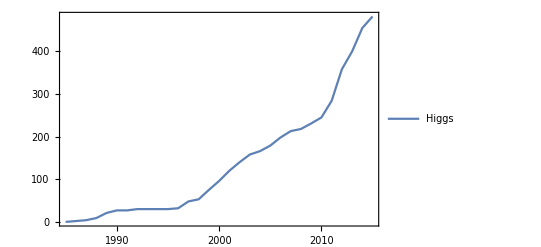

```mathematica
DateListPlot[
{occurrences["Higgs",1985, 2015]}, 
Joined->True,
PlotLegends->Placed[{"Higgs"},{0.2,0.8}], 
PlotTheme->"Detailed",
PlotRange->Full
]
```

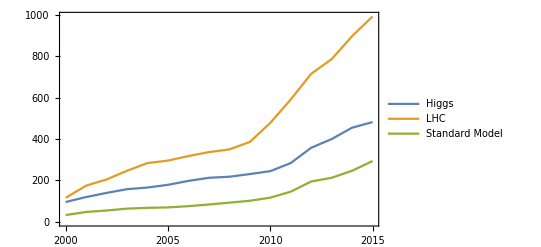

```mathematica
DateListPlot[{occurrences["Higgs",2000, 2015],occurrences["LHC", 2000, 2015],occurrences["Standard Model", 2000,2015]}, 
Joined->True, 
PlotLegends->Placed[{"Higgs", "LHC","Standard Model"},{0.2,0.8}], 
PlotTheme->"Detailed",
PlotRange->Full
]
```

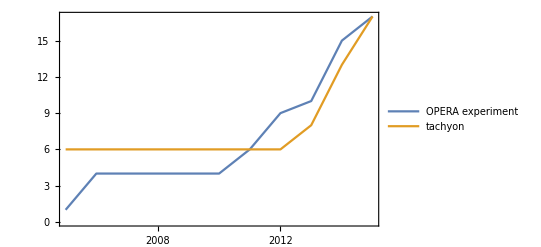

```mathematica
DateListPlot[{occurrences["OPERA",2005,2015], occurrences["tachyon",2005,2015]}, 
Joined->True, 
PlotLegends->Placed[{"OPERA experiment", "tachyon"},{0.2,0.8}], 
PlotTheme->"Detailed",
PlotRange->Full
]
```

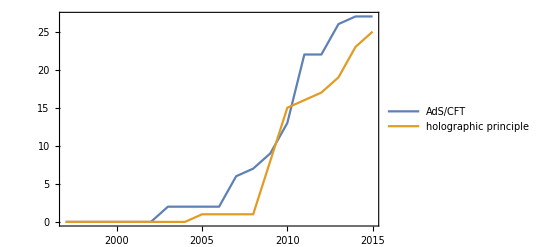

```mathematica
DateListPlot[{occurrences["AdS/CFT",1997,2015],occurrences["holographic",1997,2015]}, 
Joined->True, 
PlotLegends->Placed[{"AdS/CFT", "holographic principle"},{0.2,0.8}], 
PlotTheme->"Detailed",
PlotRange->Full
]
```

## Citation graphs of paper with more than N citations about a given topic

We select the papers with more than 50 citations:

```mathematica
citationsData=Select[
pubdata,
Length[#["citations"]]≥ 20&
];
```

and we define an association between ID and citations list, authors, abstracts and titles:

```mathematica
$idWithCitations=
AssociationThread[
Lookup[#,"recid"],
Lookup[#,"citations"]
]&@Normal@citationsData;
```

```mathematica
idWithCitations=
#recid->#citations&/@Normal@citationsData//Association ;
idAuthor=#recid->#authors&/@Normal@citationsData//Association ;
idAbstract=#recid->#abstract&/@Normal@citationsData//Association ;
idTitle=#recid->#title&/@Normal@citationsData//Association ;
idCreationDate=#recid->#CreationDate&/@Normal@citationsData//Association ;
```

```mathematica
equalDates[date2_][date1_]:=MatchQ[
DateObject[DateValue[date1,"Year"]],DateObject[DateValue[date2,"Year"]]
]
```

```mathematica
compareDates[date1_,date2_]:=If[DateOverlapsQ[date1,date2],DateObject[{DateValue[date1,"Year"]}],date1< date2];
compareDates[date1_][date2_]:=compareDates[date2,date1];
compareYears[date1_,date2_]:=date1≤date2;
compareYears[date1_Integer][date2_]:=compareYears[date2,date1];
compareYears[date1_DateObject]:=compareYears[DateValue[date1,"Year"]];
```

We select those papers containing the keyword in the abstract and define the association ID -> Citations:

```mathematica
idAbstractswithWord[words_String]:=Keys@Select[idAbstract,StringContainsQ[words]] 
idWithCitationsandTopic[words_String]:=Thread[#->Lookup[idWithCitations,#]]&@idAbstractswithWord[words]
```

and plot the graph associated to that keyword (representing a concept/topic)

```mathematica
vertexmostcited[n_Integer]:=Keys@Select[idWithCitations,Length[#]≥ n&]
graphTopic=Graph[
Thread/@idWithCitationsandTopic["BMS group"]//Flatten,
DirectedEdges->False, 
VertexStyle->Red,
VertexSize->Automatic,
ImageSize->Automatic
];
```

We highlight the most cited papers:

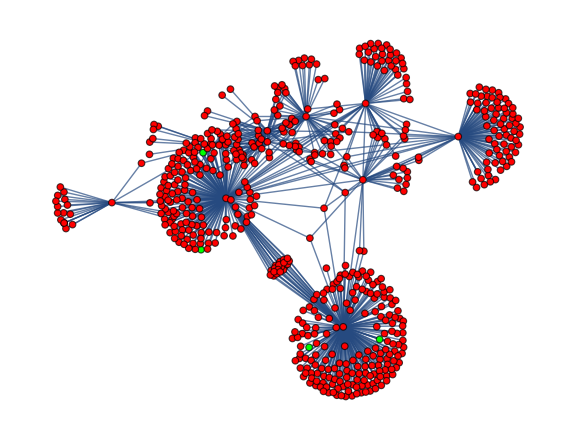

```mathematica
HighlightGraph[
graphTopic,
Style[vertexmostcited[300],Green],
ImageSize->Large
]
```

```mathematica
(*{FindVertexCut[graphTopic],idAuthor@First@FindVertexCut[graphTopic],idTitle@First@FindVertexCut[graphTopic],idAbstract@First@FindVertexCut[graphTopic]}*)
```

```mathematica
(*{GraphHub[graphTopic],idAuthor@First@GraphHub[graphTopic],idTitle@First@GraphHub[graphTopic],idAbstract@First@GraphHub[graphTopic]}*)
```

We define the highly central vertices:

```mathematica
highlyCentral[graph_]:=Pick[
VertexList@graph,
GreaterThan[10]/@DegreeCentrality@graph
]
```

```mathematica
(*highlyCentral[graphTopic]
GraphHub[graphTopic]
FindVertexCut[graphTopic]*)
```

and display all the graph communities:

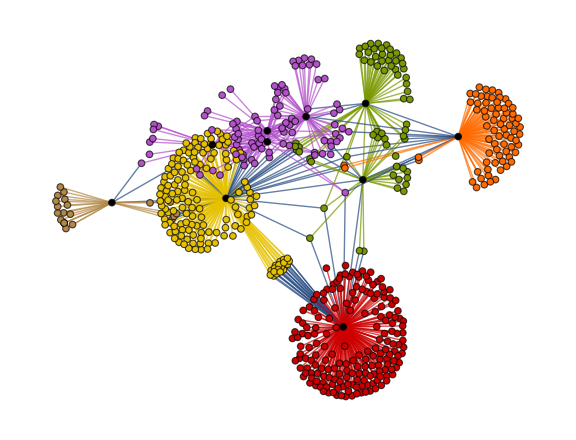

```mathematica
HighlightGraph[
HighlightGraph[
graphTopic,
Map[Subgraph[graphTopic,#]&, FindGraphCommunities[graphTopic,Method->"Centrality"]]],
Style[highlyCentral[graphTopic],Black], 
ImageSize->Large
]
```

```mathematica
HighlightGraph[
HighlightGraph[Graph3D[graphTopic],
Map[Subgraph[Graph3D[graphTopic],#]&, 
FindGraphCommunities[Graph3D[graphTopic],
Method->"Centrality"]]],
Style[highlyCentral[Graph3D[graphTopic]],Black], 
ImageSize->Large
]
```

-Graphics3D-

## Citation graphs of paper with more than N citation about a given topic in a given year

We select papers by date and topic

```mathematica
idAbstractswithDateTopic[date_,words_String]:=Intersection[Keys@Select[idCreationDate,equalDates[date]],Keys@Select[idAbstract,StringContainsQ[words]]]
idCitations[date_,words_String]:=Thread[#->Lookup[idWithCitations,#]]&@idAbstractswithDateTopic[date,words]
```

and we consider only the connected part of the graph

```mathematica
connectedg[graph_]:=graph//EdgeList//ReplaceAll[DirectedEdge->UndirectedEdge]//
Select[#,Not@*FreeQ[Alternatives@@First@ConnectedComponents[#]]]&;
```

### Example: citation graphs about holography in 2001 and 2002

```mathematica
citsAssotiation=idCitations[DateObject[{2002}],"holography"];
assograph=Thread/@citsAssotiation//Flatten;
```

```mathematica
g=Graph[assograph,GraphLayout->"RadialEmbedding",DirectedEdges->False, VertexStyle->Red,VertexSize->Automatic,ImageSize->Large];
```

```mathematica
connectedGraph=Graph[connectedg[g],GraphLayout->"RadialEmbedding"];
```

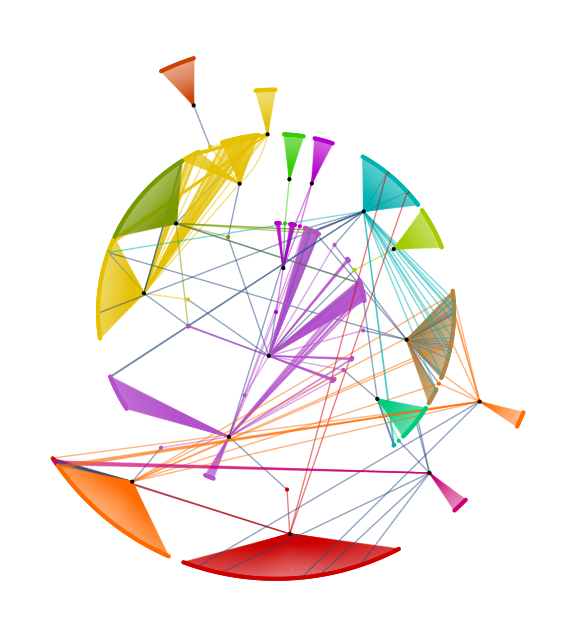

```mathematica
CommunityConnectedGraph=HighlightGraph[
HighlightGraph[connectedGraph,Map[Subgraph[connectedGraph,#]&, FindGraphCommunities[connectedGraph,Method->"Centrality"]]],
Style[highlyCentral[connectedGraph],Black], ImageSize->Large
]
```

```mathematica
HighlightGraph[
HighlightGraph[Graph3D[connectedg[g]],Map[Subgraph[Graph3D[connectedg[g]],#]&, FindGraphCommunities[Graph3D[connectedg[g]],Method->"Centrality"]]],
Style[highlyCentral[Graph3D[connectedg[g]]],Black], ImageSize->Large]
```

-Graphics3D-

```mathematica
citsAssotiation=idCitations[DateObject[{2001}],"holography"];
assograph=Thread/@citsAssotiation//Flatten;
```

```mathematica
g2=Graph[assograph,GraphLayout->"RadialEmbedding",DirectedEdges->False, VertexStyle->Red,VertexSize->Automatic,ImageSize->Large];
```

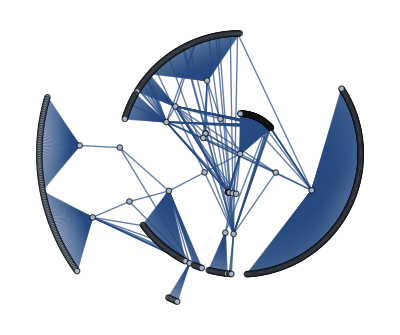

```mathematica
connectedGraph=Graph[connectedg[g2],GraphLayout->"RadialEmbedding"]
```

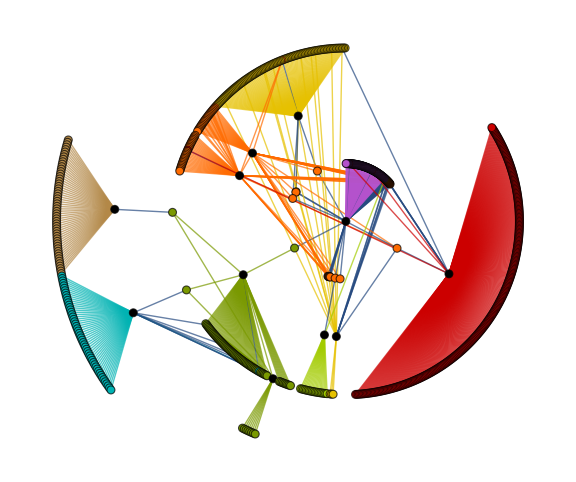

```mathematica
CommunityConnectedGraph=HighlightGraph[
HighlightGraph[connectedGraph,Map[Subgraph[connectedGraph,#]&, FindGraphCommunities[connectedGraph,Method->"Centrality"]]],
Style[highlyCentral[connectedGraph],Black], ImageSize->Large
]
```

```mathematica
HighlightGraph[
HighlightGraph[Graph3D[connectedg[g2]],Map[Subgraph[Graph3D[connectedg[g2]],#]&, FindGraphCommunities[Graph3D[connectedg[g2]],Method->"Centrality"]]],
Style[highlyCentral[Graph3D[connectedg[g2]]],Black], ImageSize->Large]
```

-Graphics3D-

## Time evolution of citation graphs

We select those papers about a given TOPIC published up to YEAR:

```mathematica
idCreationYear=DateValue[#,"Year"]&/@idCreationDate;
```

```mathematica
idAbstractswithDateTopic[date_,words_String]:=Intersection[Keys@Select[idCreationYear,compareYears[date]],Keys@Select[idAbstract,StringContainsQ[words]]]
idCitations[date_,words_String]:=Thread[#->Lookup[idWithCitations,#]]&@idAbstractswithDateTopic[date,words]
```

### Example: AdS/CFT

```mathematica
timeEvo=idCitations[#,"AdS/CFT"]&/@DateRange[DateObject[{1998}],DateObject[{2008}],Quantity[1,"Years"]];
```

```mathematica
timeEvoPruned=
With[{edges=Flatten[Thread/@#]},
Select[edges,Not@*MemberQ[Alternatives@@#]]&@
Pick[VertexList@edges,LessThan[20]/@VertexDegree[edges]]
]&/@timeEvo;
```

```mathematica
g=Table[Graph[timeEvoPruned[[i]],DirectedEdges->False, VertexStyle->Red,VertexSize->Small,ImageSize->Automatic],{i,1,Length[timeEvoPruned]}];
```

```mathematica
CommunityConnectedGraph=Table[
HighlightGraph[g[[i]],Map[Subgraph[g[[i]],#]&, FindGraphCommunities[g[[i]],Method->"Centrality"]]],{i,1,Length[g]}]
```

```mathematica
ListAnimate[CommunityConnectedGraph]
```

### Example: BMS group

```mathematica
timeEvo=idCitations[#,"BMS group"]&/@DateRange[DateObject[{1978}],DateObject[{2008}],Quantity[1,"Years"]];
```

```mathematica
timeEvoPruned=
With[{edges=Flatten[Thread/@#]},
Select[edges,Not@*MemberQ[Alternatives@@#]]&@
Pick[VertexList@edges,LessThan[0]/@VertexDegree[edges]]
]&/@timeEvo;
```

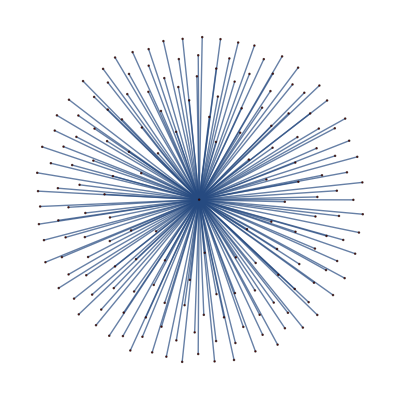
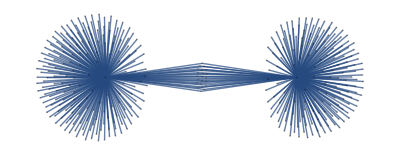
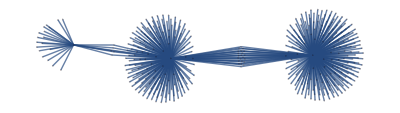
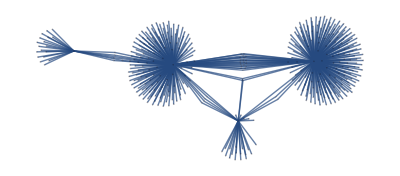
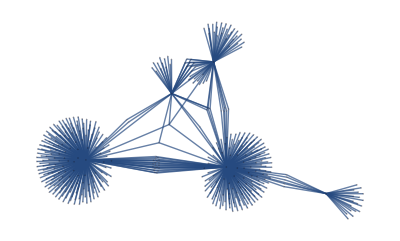
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
g=Table[Graph[timeEvoPruned[[i]],DirectedEdges->False, VertexStyle->Red,VertexSize->Small,ImageSize->Automatic],{i,1,Length[timeEvoPruned]}]
```

```mathematica
CommunityConnectedGraph=Table[
HighlightGraph[g[[i]],Map[Subgraph[g[[i]],#]&, FindGraphCommunities[g[[i]],Method->"Centrality"]]],{i,1,Length[g]}];
```

```mathematica
ListAnimate[CommunityConnectedGraph]
```

```mathematica
HighlightGraph[
HighlightGraph[Graph3D[timeEvoPruned[[31]],DirectedEdges->False],Map[Subgraph[Graph3D[timeEvoPruned[[31]]],#]&, FindGraphCommunities[Graph3D[timeEvoPruned[[31]]],Method->"Centrality"]]],
Style[FindVertexCut[graphTopic],Green], ImageSize->Large]
```

-Graphics3D-

```mathematica
HighlightGraph[Graph3D[timeEvoPruned[[31]],DirectedEdges->False],Style[FindVertexCut[graphTopic],Green]]
```

-Graphics3D-

```mathematica
FindVertexCut[graphTopic]
```

## Authors’ cloud

```mathematica
idAbstractswithDateTopic[date_,words_String]:=Intersection[Keys@Select[idCreationDate,compareDates[date]],Keys@Select[idAbstract,StringContainsQ[words]]]
idCitations[date_,words_String]:=Thread[#->Lookup[idWithCitations,#]]&@idAbstractswithDateTopic[date,words]
```

```mathematica
authorCloud[date_,words_String]:=Lookup[idAuthor,#]&@Keys@idCitations[date,words]//Flatten//WordCloud
```

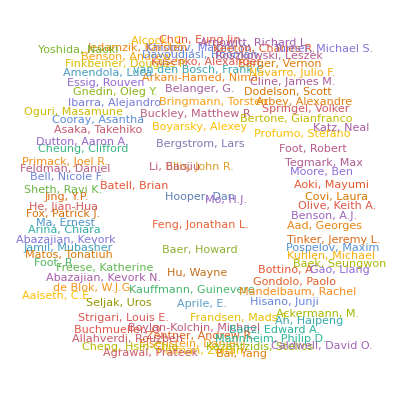

```mathematica
authorCloud[DateObject[{2015}],"dark matter"]
```

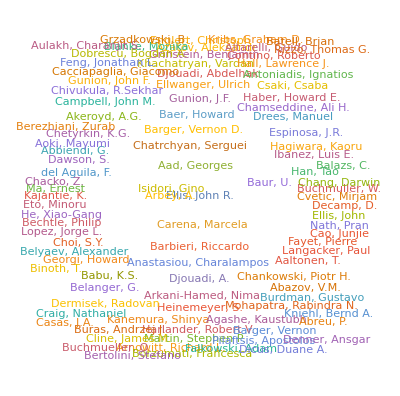

```mathematica
authorCloud[DateObject[{2015}],"Higgs"]
```

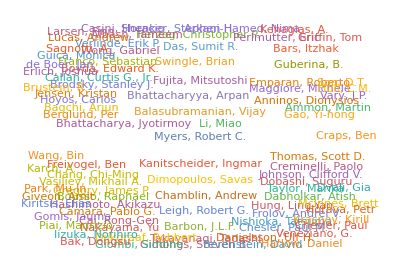

```mathematica
authorCloud[DateObject[{2015}],"holography"]
```

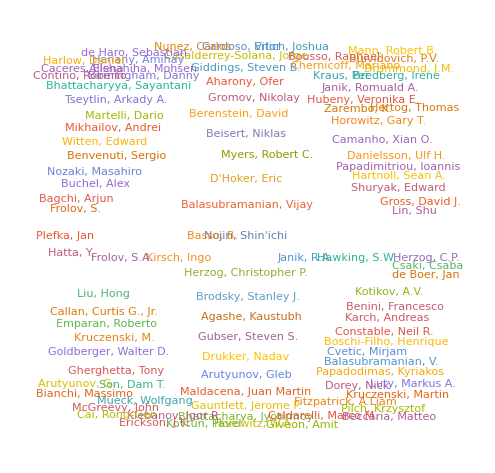

```mathematica
authorCloud[DateObject[{2015}],"AdS/CFT"]
```

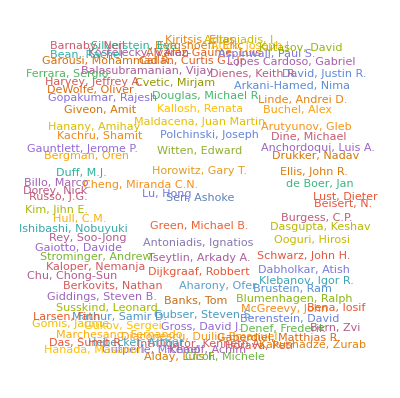

```mathematica
authorCloud[DateObject[{2015}],"string theory"]
```

## Export notebook on Cloud

```mathematica
CopyFile[
"Desktop/WSS17_project/WSS17_OLIVERI.nb",
CloudObject[
"WSS17_OLIVERI.nb",
Permissions->"Public"
]
]
```

CloudObject[https://www.wolframcloud.com/objects/user-cd1f147f-1b1f-420a-b028-659205f9c727/WSS17_OLIVERI.nb,Permissions→Public]